```mathematica
D[ρ[r]*u[r],r] + ρ[r]*u[r]/r
D[ρ[r]*u[r]^2 + p[r],r] + ρ[r]*u[r]^2/r + p[r]/r
D[ρ[r]*u[r]^3 /2+ γ*u[r]*p[r]/(γ-1),r] + ρ[r]*u[r]^3/(2*r) +γ*u[r] p[r]/(γ-1)/r
```

(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]

p[r]/r+(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]

(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]

```mathematica
Решаем
```

```mathematica
γ=2.0;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,p[r]/r+(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]-(-5.0*u[r]*ρ[r])==0,(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]-(-5.0*u[r]^2*ρ[r])==0,u[0.05]==1,ρ[0.05]==1,p[0.05]==0.05},{ρ,u,p},{r,0.05,0.13}]
```

NDSolve::ndsz: At r == 0.120752, step size is effectively zero; singularity or stiff system suspected.

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

```mathematica
ρ[r0]/. s
```

{0.875293}

```mathematica
DD = 0;
r0=0.1;
ro1 =ρ[r0]/. s
p1 = p[r0]/. s
u1 = u[r0]/. s
g = 2.0;
ss = NSolve[ro1*(u1-DD)==ro*(u-DD)&&ro1*u1*(u1 - DD) + p1 == ro*u*(u - DD)+ p&& ro1*(u1 - DD)*(p1/(ro1*(g-1)) + u1^2/2) + p1 * u1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals]
```

{0.717245}

{0.051444}

{0.697112}

{{p→0.215223,ro→1.35298,u→0.369555},{p→0.051444,ro→0.717245,u→0.697112}}

```mathematica
r0=0.1;
g1=u/. ss[[1]];
g2=ro/. ss[[1]];
g3=p/. ss[[1]];
sss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,p[r]/r+(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]-(-5.0*u[r]*ρ[r])==0,(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]-(-5.0*u[r]^2*ρ[r])==0,u[r0]==g1,ρ[r0]==g2,p[r0]==g3},{ρ,u,p},{r,r0,2}]
```

NDSolve::ndsz: At r == 0.113032, step size is effectively zero; singularity or stiff system suspected.

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

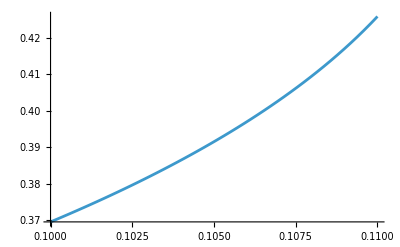

```mathematica
Plot[Evaluate[u[r]/. sss],{r,r0,0.11},PlotRange->All]
```

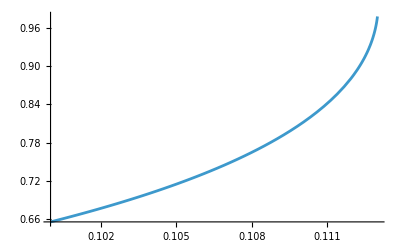

```mathematica
Plot[Evaluate[(u[r]/Sqrt[γ*p[r]/ρ[r]])/. sss],{r,r0,0.113},PlotRange->All]
```

```mathematica
γ=5/3;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,p[r]/r+(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]-(-2.1*u[r]*ρ[r])==0,(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]-(-2.1*u[r]^2*ρ[r])==0,u[0.50745]==1,ρ[0.50745]==1,p[0.50745]==2},{ρ[r],u[r],p[r]},{r,0.50745,1}]
```

NDSolve::ndsz: At r == 0.739335, step size is effectively zero; singularity or stiff system suspected.

{{ρ[r]→InterpolatingFunction[…][r],u[r]→InterpolatingFunction[…][r],p[r]→InterpolatingFunction[…][r]}}

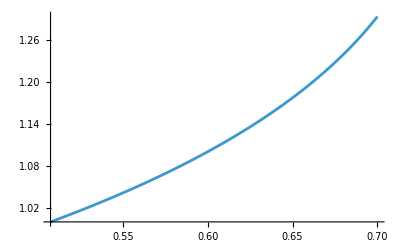

```mathematica
Plot[Evaluate[u[r]/. s],{r,0.50745,0.7},PlotRange->All]
```

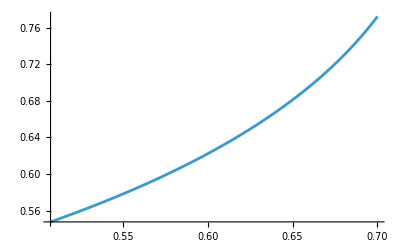

```mathematica
Plot[Evaluate[(u[r]/Sqrt[γ*p[r]/ρ[r]])/. s],{r,0.50745,0.7},PlotRange->All]
```